## Matrix Element calculation

```mathematica
nmax = 10;η = 0.2; τ = 1/(1.84 10^6)
```

5.43478×10^-7

```mathematica
M[n_,nt_] :=Integrate[Sin[θ]/2 Integrate[Exp[-t/τ]/τ Abs[∑_(m=1)^nmax √((n!)/((n+nt-n)!))(ⅈ η Cos[θ])^(nt-n)LaguerreL[n,nt-n,(η Cos[θ])^2]*√((n!)/((n+nt-n)!))(ⅈ η 1)^(nt-n)LaguerreL[n,nt-n,(η 1)^2]]^2,{t,0,Infinity}],{θ,0, Pi}]
```

```mathematica
M[2,1]
```

0.00800013

```mathematica
Mat = Table[M[n,nt],{n,1,nmax},{nt,1,nmax}]
```

{{89.7319,0.200003,0.000110023,2.5094×10^-8,3.06955×10^-12,2.32501×10^-16,1.19404×10^-20,4.42459×10^-25,1.23773×10^-29,2.70502×10^-34},{0.200003,80.3994,0.42177,0.000420272,1.51327×10^-7,2.68302×10^-11,2.77862×10^-15,1.87×10^-19,8.79225×10^-24,3.04251×10^-28},{0.000110023,0.42177,71.9246,0.702562,0.00111472,5.84007×10^-7,1.41864×10^-10,1.92764×10^-14,1.64734×10^-18,9.58641×10^-23},{2.5094×10^-8,0.000420272,0.702562,64.2358,1.02828,0.00239463,1.72549×10^-6,5.51075×10^-10,9.52013×10^-14,1.00776×10^-17},{3.06955×10^-12,1.51327×10^-7,0.00111472,1.02828,57.2666,1.3866,0.0044806,4.26137×10^-6,1.73389×10^-9,3.71489×10^-13},{2.32501×10^-16,2.68302×10^-11,5.84007×10^-7,0.00239463,1.3866,50.9563,1.76681,0.00760338,9.24917×10^-6,4.67706×10^-9},{1.19393×10^-20,2.77862×10^-15,1.41864×10^-10,1.72549×10^-6,0.0044806,1.76681,45.2486,2.15967,0.0119961,0.0000182077},{4.34877×10^-25,1.86984×10^-19,1.92764×10^-14,5.51075×10^-10,4.26137×10^-6,0.00760338,2.15967,40.0918,2.55723,0.0178877},{5.1972×10^-29,8.64158×10^-24,1.6472×10^-18,9.52014×10^-14,1.73389×10^-9,9.24917×10^-6,0.0119961,2.55723,35.4385,2.95274},{9.7732×10^-27,1.27755×10^-27,9.42212×10^-23,1.00767×10^-17,3.7149×10^-13,4.67706×10^-9,0.0000182077,0.0178877,2.95274,31.245}}

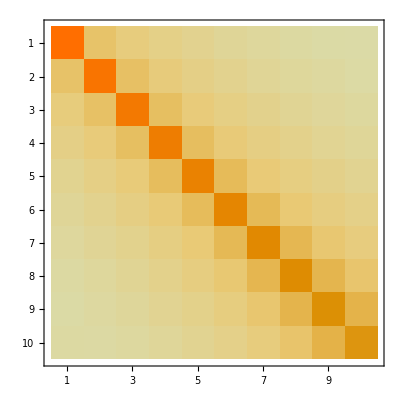

```mathematica
MatrixPlot[Mat]
```

```mathematica
Mat = {{89.73189120000002,0.2000032085333334,0.00011002339486927706,2.509395207314289*^-8,3.0695515946391326*^-12,2.3250055277701026*^-16,1.1940374668425611*^-20,4.424592855848029*^-25,1.2377275732321855*^-29,2.7050153862222876*^-34},{0.20000320853333353,80.3993918426986,0.42176986859201127,0.0004202719902583808,1.5132663420174065*^-7,2.6830212412543234*^-11,2.778615863887534*^-15,1.8700047808518214*^-19,8.792254592656171*^-24,3.042512759827579*^-28},{0.00011002339486928319,0.4217698685920112,71.92462014254228,0.7025623820717465,0.0011147200944999723,5.840071353620498*^-7,1.4186359814798123*^-10,1.927640601808704*^-14,1.6473445778916955*^-18,9.586405027278855*^-23},{2.5093952073193054*^-8,0.00042027199025840436,0.7025623820717465,64.2357646370139,1.0282778686958816,0.0023946294240447677,1.725493862251961*^-6,5.510751522545706*^-10,9.520128853790232*^-14,1.0077623425949352*^-17},{3.0695515914077746*^-12,1.513266342020434*^-7,0.0011147200945000376,1.028277868695882,57.26664226072516,1.3865964393346133,0.004480598620139658,4.261365742966132*^-6,1.7338927736595383*^-9,3.71489168840939*^-13},{2.32500784847032*^-16,2.6830212384298715*^-11,5.840071353632175*^-7,0.002394629424044907,1.3865964393346124,50.95628622259219,1.7668107702829745,0.007603375809215791,9.249172745226676*^-6,4.677056482052234*^-9},{1.1939307864547287*^-20,2.7786186373581163*^-15,1.4186359799863958*^-10,1.7254938622554135*^-6,0.004480598620139917,1.7668107702829756,45.24856183222715,2.159669298304147,0.011996076290873323,0.000018207670537881466},{4.348768556079334*^-25,1.8698377066679602*^-19,1.9276425258798086*^-14,5.510751516744465*^-10,4.2613657429746546*^-6,0.00760337580921622,2.1596692983041494,40.09180852805582,2.5572320857578186,0.017887660163669276},{5.197197497300727*^-29,8.641581622374825*^-24,1.6471973971177688*^-18,9.520138356290255*^-14,1.7338927718342476*^-9,9.249172745245187*^-6,0.011996076290874014,2.5572320857578226,35.438506460400546,2.9527384644418437},{9.773198716377846*^-27,1.277546048326997*^-27,9.42212269166648*^-23,1.0076723048192896*^-17,3.7148953964220513*^-13,4.6770564771286365*^-9,0.000018207670537917916,0.017887660163670306,2.9527384644418477,31.24496607813421}};
```

```mathematica
Master equation for Raman- 3 level system
```

```mathematica
Clear[α, η]
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ωR}, {0, ωR, -2 δ2}})
```

{{-hbar δ1,(hbar Ωn)/2,0},{(hbar Ωn)/2,0,(hbar ωR)/2},{0,(hbar ωR)/2,-hbar δ2}}

```mathematica
Γ1 = α η^2 n Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
```

```mathematica
Γo = Γ - Γ1 - Γ2;
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{n α Γ η^2 ρ33[t],0,-1/2 Γ ρ13[t]},{0,(1-α) Γ (1-(-1+2 n) η^2) ρ33[t],-1/2 Γ ρ23[t]},{-1/2 Γ ρ31[t],-1/2 Γ ρ32[t],-Γ ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
dρdt = -ⅈ/hbar(H. ρe[t]- ρe[t]. H)+ L//FullSimplify
```

{{1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t])},{-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t])},{-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}}

```mathematica
ρef = Flatten[ρe'[t]]
```

{ρ11'[t],ρ12'[t],ρ13'[t],ρ21'[t],ρ22'[t],ρ23'[t],ρ31'[t],ρ32'[t],ρ33'[t]}

```mathematica
ρef2 = Flatten[ρe[t]]
```

{ρ11[t],ρ12[t],ρ13[t],ρ21[t],ρ22[t],ρ23[t],ρ31[t],ρ32[t],ρ33[t]}

```mathematica
dρdtf= Flatten[dρdt]
```

{1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]]
```

{ρ11'[t]==1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],ρ12'[t]==1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),ρ13'[t]==1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),ρ21'[t]==-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),ρ22'[t]==1/2 (-ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t]),ρ23'[t]==-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),ρ31'[t]==-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),ρ32'[t]==-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),ρ33'[t]==-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
sol=DSolve[system,ρef2,t]
```

```mathematica
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]
```

{0==1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],0==1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),0==1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),0==-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),0==-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],0==-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),0==-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),0==-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),0==-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
system
```

```mathematica
Solve[system, ρef2]
```

{{ρ11[t]→0,ρ12[t]→0,ρ13[t]→0,ρ21[t]→0,ρ22[t]→0,ρ23[t]→0,ρ31[t]→0,ρ32[t]→0,ρ33[t]→0}}

```mathematica
no steady state solution as system is not closed, one can look at solutions with constant decay rates instead
```